# XX: Convergence

We want to quantify how fast a sequence of errors e_k≥0 converges to zero.  There are lots of properties (in addition to e_k→0) that would be useful.

Non-increasing i.e. e_(k+1)≤e_k  is great.  However, we will rarely know that this holds for an entire sequence and eventually non-increasing i.e. e_(k+1)≤e_k for all k≥K is just about as good.

### Convergence Types

Asymptotic Linear Convergence i.e. e_(k+1)<C e_k for all k≥K is only useful if C<1 and only good if C is reasonable well below 1.

Super Linear Convergence lim_(k→∞) (e_(k+1))/e_k=0.

Asymptotic Quadratic (α=2) Cubic (α=3) Convergence i.e.  e_(k+1)<C (e_k)^α     ∀k≥K  is useful for any constant C.  Lets see what this means for a general α>1.

### Discussion

Linear convergence is slow if C≈1. In practice, linear convergence is too slow unless the constant C is significantly less than one. Super linear convergence is basically linear convergence with a constant that gets smaller as you go further out in the sequence. In practice, superlinear convergence is very useful.  In practice, quadratic and cubic convergence are so fast at the end that you can hardly see them. Lets see how to think about this!

### Quadratic and Cubic Convergence

Suppose we know that e_k→0 and e_(k+1)≤C (e_k)^α. We want to get a feel for what this means.

The first step is to see why the constant C does not matter that much!

There is a constant γ>0 that eliminates C in the sense that e_(k+1)≤C (e_k)^α ⟺(γ e_(k+1))≤(γ e_k)^α. Expand the inequality with γ to get γ e_(k+1)≤(γ^α( e_k))^α. Divide through by γ and match to see that we need C=γ^(α-1)or equivalently γ=C^(1/(α-1)).

The next step is to work with the simpler inequality f_(k+1)≤(f_k)^α for f_k=γ e_k.

Chain two of them together to get f_(k+2)≤(f_(k+1))^α≤(f_k)^(2α).

Show by induction that (f_(k+r))≤(f_k)^(r α).  As a result once f_k<1 we get very rapid convergence.

Conclusion if f_k≤10^-1 then f_(k+r)≤ 10^(-α r).

Once f_k=0.1, if α=2 then f_(k+1)≤0.01, f_(k+2)≤0.001, and f_(k+8)≤10^-16≈ϵ_m

Once f_k=0.1, if α=3 then f_(k+1)≤0.001, and f_(k+1)≤10^-6 and f_(k+5)≤10^-15≈ϵ_m

## Pictures

### Linear

Linear convergence looks like a straight line on a log plot.  The slope on the log plot gives the constant ρ.

```mathematica
MaxIter=342;
{ρ1,ρ2}={0.99,0.999}; { e1,e2}={2.3,3.4};
es1=Table[e1  ρ1^i,{i,1, MaxIter}];
es2=Table[e2  ρ2^i,{i,1, MaxIter}];
TabView[{
"normal"->ListPlot[{es1,es2},GridLines->Automatic,Frame->True,PlotLegends->Automatic],
"log"->ListLogPlot[{es1,es2},GridLines->Automatic,Frame->True,PlotLegends->Automatic]
}]
```

12

### Asymptotic Linear

Real errors usually bounce around a bit before they hit an asymptotic regime. Asymptotic linear convergence eventually looks like a straight line on a log plot.  The eventual slope on the log plot gives the constant ρ.

```mathematica
m=23;
A=RandomReal[{-1,1},{m,m}]+DiagonalMatrix[RandomReal[{2,10 },m]];
b=RandomReal[{-1,1},m];
x=LinearSolve[A,b];
{U,L,dia}={UpperTriangularize[A,1],LowerTriangularize[A,-1],Diagonal[A]};
TabView[{"A"->MatrixPlot[A],"U"->MatrixPlot[U],
"L"->MatrixPlot[L],"dia"->MatrixPlot[DiagonalMatrix[dia]],
"U+L+dia"->MatrixPlot[U+L+DiagonalMatrix[dia]]}]
```

12345

Jacobi:
If A.x=b then (U+D+L).x=b and D.x=b-(U+L).x and x=D^-1.(b-(U+L).x ).

Gauss-Seidel:
If A.x=b then (U+D+L).x=b and (D+U).x=b-L.x and x=(D+U)^-1.(b-L.x ).

```mathematica
m=23;
A=RandomReal[{-1,1},{m,m}]+DiagonalMatrix[RandomReal[{2,10 },m]];
b=RandomReal[{-1,1},m];
x=LinearSolve[A,b];
{U,L,dia}={UpperTriangularize[A,1],LowerTriangularize[A,-1],Diagonal[A]};
MaxIter=11;
x0=RandomReal[{-1,1},m];
JStep[x_]:=DiagonalMatrix[1/dia].(b-(U+L).x)
GSStep[x_]:=Inverse[DiagonalMatrix[dia]+U].(b-L.x)
Jxs=NestList[JStep,x0,MaxIter];
GSxs=NestList[GSStep,x0,MaxIter];
TabView[{"Jacobi x"->MatrixPlot[Jxs],
"Gauss-Seidel x"->MatrixPlot[GSxs],
"errs"->ListLogPlot[{
Table[Norm[Jxs⟦i⟧-x],{i, MaxIter+1}],
Table[Norm[GSxs⟦i⟧-x],{i, MaxIter+1}]},
PlotLegends->{"J","GS"}]
}]
```

123

### Super Linear

Super linear convergence eventually lies below the “tangent-line” on a log plot of the errors.  Of course you can not do better than standard double precision!

The classic example is the secant method for solving f[x]=0.  Suppose I have two near by pairs {x_1,f[x_1]} and {x_2,f[x_2]} then I can approximate the derivative (somewhere in between x_1 and x_2) by m≈(f[x_1]-f[x_2])/(x_1-x_2) and I could use the secant line
	y=f[x_2]+m(x-x_2) 
to define an x_3 as the zero of the secant line i.e. f[x_2]+m(x_3-x_2)==0 or equivalently
	x_3=x_2-f[x_2]/m.
A single step of this "secant method" is easy to visualize

2.23282

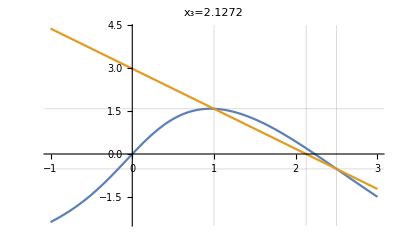

```mathematica
f[x_]:= Sin[x + ArcTan[x]]-0.4 x^2+x
xMma =x/.FindRoot[f[x]==0,{x,2}]
{x1,x2}={1.0,2.5};
m=(f[x1]-f[x2])/(x1-x2);
x3=x2-f[x2]/m;
Plot[{f[x],f[x2]+m(x-x2)},{x,-1,3},
PlotLabel->StringForm["x_3=``",x3],
GridLines->{{x1,x2,x3},{f[x1],f[x2]}}]
```

It is even relatively easy to iterate

```mathematica
Clear[x]
MaxIter=7;
SecantStep[f_][{x1_,x2_}]:= Module[{m},
m=(f[x1]-f[x2])/(x1-x2);
{x2,x2-f[x2]/m}]
SecantData=NestList[SecantStep[f],{x1,x2},MaxIter];
SecantErrs = Table[xMma-SecantData⟦i,2⟧,{i, MaxIter}];
TabView[{"Data"->TableForm[SecantData],
"Errs"-> TableForm[SecantErrs],
"LogPLot"->ListLogPlot[Abs[SecantErrs]]}]
```

123

### Asymptotic Quadratic Convergence

Asymptotic quadratic convergence ends very abruptly.  After bouncing around it goes 
	10^-p, 10^(-2p), 10^(-4p),…
of course it can not get below 10^-16 in standard double precision!

The classic example is Newton’s method for solving f[x]=0.  Suppose I have a point x_1 then I can use the tangent line 
	y=f[x_1]+f'[x_1](x-x_1) 
to define an x_2 as the zero of the secant line i.e. f[x_1]+f'[x_1](x_2-x_1)==0 or equivalently
	x_2=x_1-f[x_1]/f'[x_1].
A single step of this “Newton method” is easy to visualize

2.23282

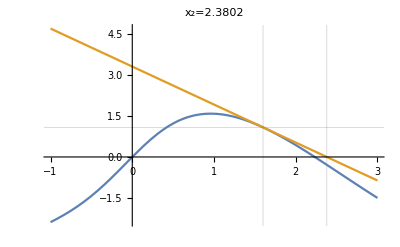

```mathematica
f[x_]:= Sin[x + ArcTan[x]]-0.4 x^2+x
xMma =x/.FindRoot[f[x]==0,{x,2}]
x1=1.6;
m=f'[x1];
x2=x1-f[x1]/m;
Plot[{f[x],f[x1]+m(x-x1)},{x,-1,3},
PlotLabel->StringForm["x_2=``",x2],
GridLines->{{x1,x2},{f[x1]}}]
```

It is also easy to code.  Quadratic convergence is very fast at the end!

```mathematica
Clear[x]
MaxIter=7;
NewtonStep[f_][x1_]:= Module[{m},
m=f'[x1];
x1-f[x1]/m]
NewtonData=NestList[NewtonStep[f],x1,MaxIter];
NewtonErrs = Table[xMma-NewtonData⟦i⟧,{i, MaxIter}];
TabView[{"Data"->TableForm[NewtonData],
"Errs"-> TableForm[NewtonErrs],
"LogPlot"->ListLogPlot[Abs[NewtonErrs]]
}]
```

123